# Quantum Error-Correction Codes

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

## Nine-Qubit Code

## Overview of Quantum Error Correction

## Stabilizer Code

### Pauli Group

### Clifford Group

### Stabilizers

### Unitary Gates in the Stabilizer Formalism

### Measurement in the Stabilizer Formalism

We discuss again quantum teleportation, this time, in the stabilizer formalism.

```mathematica
Let[Complex,c]
in=ProductState[S[3]->c@{0,1},"Label"->Ket[ψ]]
```

(c_0 0+c_1 1)_S_3

This is a quantum circuit model for quantum teleportation. It consists of three stages separated by the vertical dashed lines in the quantum circuit model. The first stage is to share the entangled pair of qubits. The second in the middle corresponds to the Bell measurement. The final stage transmits the measurement outcomes to Alice, and Alice adjusts the state of her qubit according to the classical information.

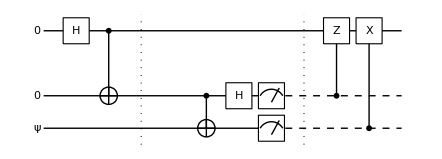

```mathematica
qc=QuantumCircuit[in,LogicalForm[Ket[],S@{1,2}],S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",CNOT[S[2],S[3]],S[2,6],{Measurement[S[2]],Measurement[S[3]]},"Separator",ControlledU[S[2],S[1,3]],ControlledU[S[3],S[1,1]],"Invisible"->S[1.5]]
```

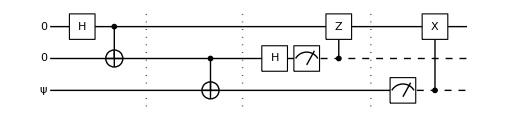

```mathematica
qc2=QuantumCircuit[
in,LogicalForm[Ket[],S@{1,2}],
S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",
CNOT[S[2],S[3]],"Separator",
S[2,6],Measurement[S[2]],ControlledU[S[2],S[1,3]],"Separator",
Measurement[S[3]],ControlledU[S[3],S[1,1]]
]
```

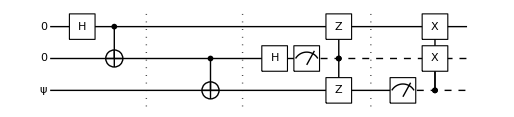

```mathematica
qc3=QuantumCircuit[
in,LogicalForm[Ket[],S@{1,2}],
S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",
CNOT[S[2],S[3]],"Separator",
S[2,6],Measurement[S[2]],
{ControlledU[S[2],S[1,3]],ControlledU[S[2],S[3,3]]},"Separator",
Measurement[S[3]],
{ControlledU[S[3],S[1,1]],ControlledU[S[3],S[2,1]]}
]
```

```mathematica
out=Table[ExpressionFor[qc3],{15}]/.c[0]*Conjugate[c[0]]+c[1]*Conjugate[c[1]]->1;
LogicalForm@QuissoFactor[#,S@{2,3}]&/@out//TableForm
```

1_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_21_S_3⊗(-c_0 0_S_1-c_1 1_S_1)
0_S_21_S_3⊗(-c_0 0_S_1-c_1 1_S_1)
0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_21_S_3⊗(-c_0 0_S_1-c_1 1_S_1)
0_S_21_S_3⊗(-c_0 0_S_1-c_1 1_S_1)

Here we investigate the procedure to remotely implement the CNOT gate.

```mathematica
Let[Integer,σ,m]
in=LogicalForm[Ket[S[1]->σ[1],S[4]->σ[4]],S@{1,2,3,4}]
out=Ket[S[1]->σ[1],S@{2,3}->m@{2,3},S[4]->Mod[σ[1]+σ[4],2]]
```

σ_1_S_10_S_20_S_3σ_4_S_4

σ_1_S_1m_2_S_2m_3_S_3(σ_1⊕σ_4)_S_4

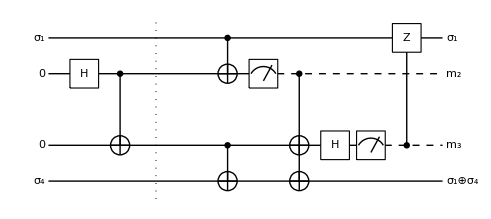

```mathematica
qc=QuantumCircuit[in,S[2,6],CNOT[S[2],S[3]],"Separator","Spacer",
{CNOT[S[1],S[2]],CNOT[S[3],S[4]]},
Measurement[S[2]],CNOT[S[2],S@{3,4}],
S[3,6],Measurement[S[3]],ControlledU[S[3],S[1,3]],out,"PortSize"->{0.65,2},"Invisible"->S[2.5]]
```

```mathematica
Quiet[new=ExpressionFor[qc],{Measurement::nonum}]
```

1/2 σ_1_S_1σ_4_S_4 (1-σ_1)+1/2 σ_1_S_1(1⊕σ_4)_S_4 σ_1

## Surface Code